## TissueCells-example.nb TissueCells, TissueEdges, TissueVertices

Example Cellzilla2D notebook.

GPL License applies. 
See http://xlr8r.info and http://cellzilla.info for further details.

```mathematica
<<Cellzilla2D.m
```

Cellzilla2D (2.3.6 (9-Nov-2012)) loaded Fri 9 Nov 2012 20:56:12
using xCellerator 0.90 and XSSA 1204002
GPL License Terms Apply

Create a tissue with a point and an edge that aren't used.

There are 8 cells in the tissue.

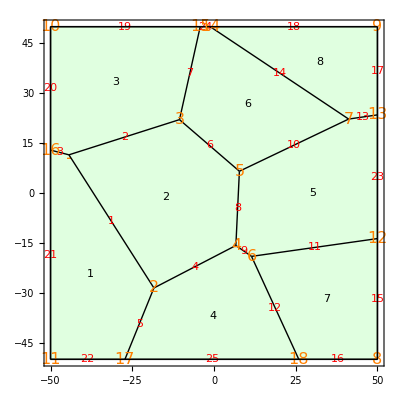

```mathematica
q=TemplateRandomSquareGrid[9, {-50, -50}, {50, 50}];
Print["There are ", NTissueCells[q], " cells in the tissue."];  
ShowTissue[q, "CellNumbers"-> True, Frame-> True, "EdgeNumbers"-> True, "EdgeNumberStyle"-> {Red, Background-> Yellow}, "VertexNumbers"-> True, "VertexNumberStyle"-> {Orange, FontSize-> 16}]
```

```mathematica
q
```

Tissue[{{-44.3734,11.4757},{-18.3812,-28.5506},{-10.5572,22.0532},{6.68829,-15.7783},{7.76841,6.53991},{11.4767,-19.0486},{41.1851,22.2244},{50,-50},{50,50},{-50,50},{-50,-50},{50.,-13.7003},{50.,23.4826},{-1.16878,50.},{-4.21177,50.},{-50.,12.8936},{-27.2449,-50.},{25.9386,-50.}},{{1,2},{1,3},{1,16},{2,4},{2,17},{3,5},{3,15},{4,5},{4,6},{5,7},{6,12},{6,18},{7,13},{7,14},{8,12},{8,18},{9,13},{9,14},{10,15},{10,16},{11,16},{11,17},{12,13},{14,15},{17,18}},{{22,5,1,3,21},{1,4,8,6,2},{20,3,2,7,19},{25,12,9,4,5},{23,13,10,8,9,11},{24,7,6,10,14},{11,12,16,15},{18,14,13,17}}]

```mathematica
TissueVertices[q]
```

{{-44.3734,11.4757},{-18.3812,-28.5506},{-10.5572,22.0532},{6.68829,-15.7783},{7.76841,6.53991},{11.4767,-19.0486},{41.1851,22.2244},{50,-50},{50,50},{-50,50},{-50,-50},{50.,-13.7003},{50.,23.4826},{-1.16878,50.},{-4.21177,50.},{-50.,12.8936},{-27.2449,-50.},{25.9386,-50.}}

```mathematica
TissueEdges[q]
```

{{1,2},{1,3},{1,16},{2,4},{2,17},{3,5},{3,15},{4,5},{4,6},{5,7},{6,12},{6,18},{7,13},{7,14},{8,12},{8,18},{9,13},{9,14},{10,15},{10,16},{11,16},{11,17},{12,13},{14,15},{17,18}}

```mathematica
TissueCells[q]
```

{{22,5,1,3,21},{1,4,8,6,2},{20,3,2,7,19},{25,12,9,4,5},{23,13,10,8,9,11},{24,7,6,10,14},{11,12,16,15},{18,14,13,17}}